```mathematica
(*here I'm defining some functions,which will simplify further calculations*)(*this is the initial system with c1=1,and c2 is a parameter*)discF:=Function[{x[n+1],y[n+1]}=={Sqrt[y[n]]-y[n],Sqrt[x[n]/#]-x[n]}]

(*function for y-coordinate of equilibrium position*)
EqYF:=Function[1/(1+#)^2]

(*function for x-coordinate of equilibrium position*)
EqXF:=Function[#/(1+#)^2]
```

WARNING

This piece of code takes approximately 15 min on my laptop to compute

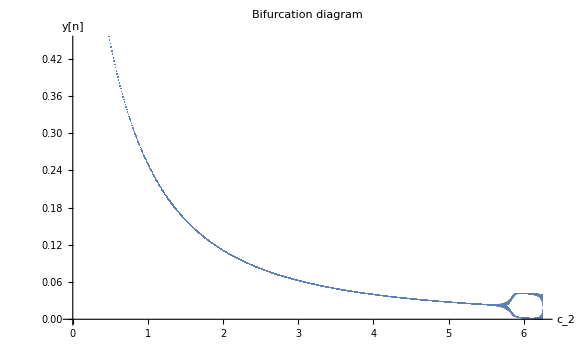

```mathematica
(*Bifurcation diagram*)(*On the y-axes I am plotting values of y[n],n in (Cut,Nodes)*)(*On the x-axes I am plotting values of c2,which stands for c2/c1 as long as c1=1*)(*On the graph below we definitely can see bifurcation neer 6*)Print[Style[WARNING,18,Red]]

Print[Style["This piece of code takes approximately 15 min on my laptop to compute",18,Red]]
Nodes=300;
Cut=100;
b=Table[temp,{temp,0.2,6.5,0.01}];
(*for detailed graph*)
(*b1=Table[temp,{temp,6,6.7,0.001}];*)a=Table[RecurrenceTable[{discF[temp],x[0]==0.01,y[0]==0.01},{x,y},{n,1,Nodes}][[;;,2]],{temp,0.2,6.5,0.01}];
(*a1=Table[RecurrenceTable[{discF[temp],x[0]==0.01,y[0]==0.01},{x,y},{n,1,Nodes}][[;;,2]],{temp,6,6.7,0.001}];*)
res={};
For[i=1,i<Length[b],i++,For[j=Cut,j<(Nodes),j++,AppendTo[res,{b[[i]],a[[i,j]]}]]]
ListPlot[res,ImageSize->Large,PlotStyle->AbsolutePointSize[.01],AxesLabel->{"c_2","y[n]"},PlotLabel->"Bifurcation diagram"]


(*res1={};

For[i=1,i<Length[b1],i++,For[j=Cut,j<(Nodes),j++,AppendTo[res1,{b1[[i]],a1[[i,j]]}]]]

ListPlot[res1,ImageSize->Large,PlotStyle->AbsolutePointSize[.01],AxesLabel->{"c_2","y[n]"},PlotLabel->"Bifurcation diagram (near c_2 = 6)"]*)
```